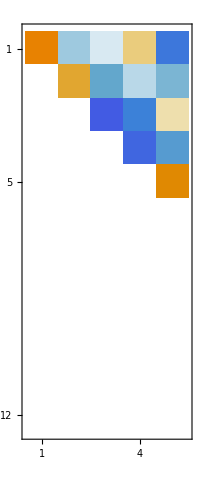

```mathematica
{m,n}={12,5}; 
A=A0=RandomReal[{-1,1},{m,n}];
F[AIn_]:=Module[{A=AIn,v,x},
Do[
x=A[[k;;m,k]];
v=x; v[[1]]+=Sign[x[[1]]]Norm[x];
v=v/Norm[v];
A[[k;;m,k;;n]]-=2KroneckerProduct[v,v].A[[k;;m,k;;n]],
{k,1,n}];
A]
A=F[A0];
MatrixPlot[Chop[A]]
```